Quantum algorithm for the Vlasov equation

Alexander Engel, Graeme Smith, and Scott E. Parker
Phys. Rev. A 100, 062315

Notebook: Óscar Amaro, March 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce the results from the paper, namely the damping of the Electric field.

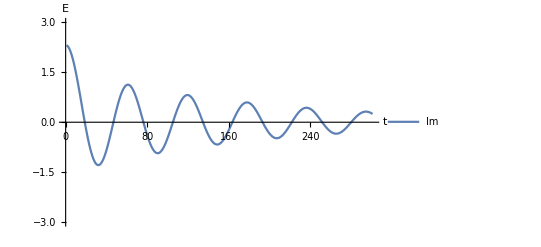

```mathematica
(* clear variables *)
Clear[k,Nv,n,vmax,Δv,v,Fj,Gj,Etil,ket,ketbra,αj,H]

(* "Dirac" to vector *)
ket[x_,n_]:=Module[{y,res,i,η},
res=Table[0,{i,0,2^n-1}];
res[[x+1]]=1;
Return[res]
]
ketbra[x_,y_]:=Transpose[{x}].{y}

(* parameters *)
n=5;
k=0.4;
Nv=2^n;
vmax=4.5;
tmax=8π;
Δv=2 vmax/(Nv-1);
v[j_]:= -vmax+2vmax (j)/(Nv-1)
Fj[j_]:=1/(√(2π))Exp[-1/2 v[j]^2]
Gj[j_]:=1/(√(2π))Exp[-1/2 v[j]^2]
αj[j_]:=Sqrt[Δv Gj[j]]
Etil=I/k Sum[Fj[i],{i,0,Nv-1}]Δv;

(* Hamiltonian *)
getH[n_]:=Sum[v[j](k ketbra[ket[j,n+1],ket[j,n+1]]+αj[j](ketbra[ket[j,n+1],ket[2^n,n+1]]+ketbra[ket[2^n,n+1],ket[j,n+1]]) ),{j,0,2^n-1}];
H=getH[n];

(* initial state *)
x0=(  Sum[Fj[j] ket[j,n+1],{j,0,Nv-1}]+Etil ket[Nv,n+1]  );
η=Sqrt[Conjugate[x0].x0];
x0= x0/η;

(* time evolve *)
tdim=300;
dt = tmax/tdim;
x=x0;
Et={};tlst={};
U=MatrixExp[-I H dt];
xnorm={};
For[t=0,t≤tdim,t++,
x=U.x;
(* x[[2^n+1]] is the position of the electric field *)
AppendTo[tlst,t dt];
AppendTo[Et,x[[2^n+1]]];
(* check normalization*)
AppendTo[xnorm,Sqrt[Conjugate[x].x]]
]
(* plot *)
EtImRe=Im[Et]+Re[Et];
ListPlot[(EtImRe)/k,Joined->True,PlotRange->{-3,+3},PlotLegends->{"Im"},AxesLabel->{"t","E"}]
```

```mathematica
(* create dataset *)
data=Transpose[{tlst,EtImRe}];
(* fit to A Exp[-γ t]Cos[ω t -ρ] *)
nlm=NonlinearModelFit[data,A Exp[-γ tt]Cos[ω tt -ρ],{A,γ,ω,ρ},tt]
(* parameters *)
nlm[[1,2]]
(* compare with numerical integration of dispersion relation *)
(* γ=0.06613 ω=1.28506 *)
```

FittedModel[0.740882 ⅇ^(-0.0819993 tt) Cos[0.315333-1.29163 tt]]

{A→0.740882,γ→0.0819993,ω→1.29163,ρ→0.315333}

True

(-1.8 | 0. | 0. | 0. | -0.00969376 | 0. | 0. | 0.
0. | -1.68387 | 0. | 0. | -0.0170636 | 0. | 0. | 0.
0. | 0. | -1.56774 | 0. | -0.0286598 | 0. | 0. | 0.
0. | 0. | 0. | -1.45161 | -0.0458971 | 0. | 0. | 0.
-0.00969376 | -0.0170636 | -0.0286598 | -0.0458971 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

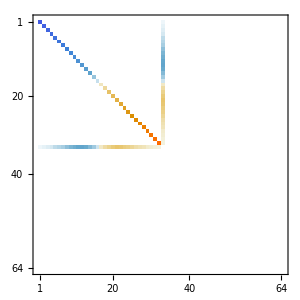

0.000625404 ⅇ^(1/2 (1.30645-0.0421436 j) j) (-15.5+1. j)

```mathematica
(* confirm U is unitary *)
UnitaryMatrixQ[U]

(* most entries are 0 *)
getH[2]//MatrixForm
(* plot matrix *)
MatrixPlot[H,ImageSize->300]

(* explicit form of vj αj *)
Refine[v[j]αj[j]//Simplify,j>0]
```